## Example usage of Rational Interpolation

The purpose of this package is to find a polynomial approximation to a function or set of points {x_{i},y_{i}} by generating a set of orthogonal polynomials to construct the numerator and denominator polynomials of the rational function r_{n,m} = p_{n}/q_{m} with at least one of p,q being monic..
Algorithm constructed based on the paper: https://doi.org/10.2307/2008359

### Example using y-points:

#### Valid Interpolation

The goal of this package is to find a set of points  that approximate a polynomial function r_{n,m}. With this package, you can simply specify a set of x points and y points and the degree you want each polynomial to be:

```mathematica
xi = Table[i, {i,1, 4, 1/2}]
yi = Table[RandomReal[{-3,3}], {i, -3,3}]
n=2;m=3;
```

{1,3/2,2,5/2,3,7/2,4}

{-2.48548,1.26909,2.08906,-2.96332,-0.17465,-1.48416,0.498817}

Let’s find a rational function that approximates these points

-0.0011552

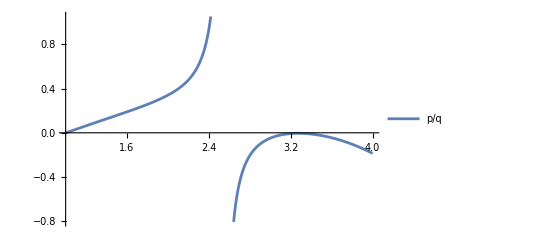

```mathematica
{p,q}=PerformRationalInterpolation[xi, yi, n,m];
(p/q )/.x->xi[[1]] (*Verify*)
Plotpq[p,q,xi]
```

We can then see that our equations are:

```mathematica
p//N
q//N
```

-7.63689+12.2778 x-5.36523 x^2+0.711428 x^3

20.9969-10.8101 x+x^2

Exact values are also valid inputs, at the cost of computation time.

{1,3/2,2,5/2,3,7/2,4}

{-4/5,-14/5,11/5,-34/5,1/5,16/5,-4/5}

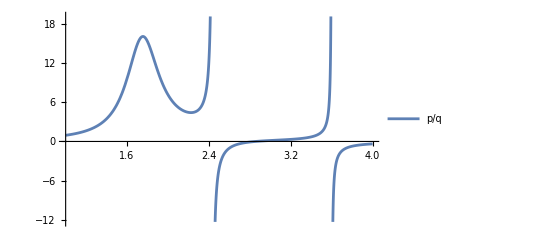

```mathematica
xi = Table[i, {i,1, 4, 1/2}]
yi = Table[(1/5)+RandomInteger[{-8,8}], {i, -3,3}]
n=4;m=3;
{p,q}=PerformRationalInterpolation[xi, yi, n,m];
Plotpq[p,q,xi]
```

```mathematica
p
q
```

72544/11655-(68861 x)/11655+(23711 x^2)/11655-(2974 x^3)/11655

402227/14870-(292853 x)/5948+(979261 x^2)/29740-(14167 x^3)/1487+x^4

#### Invalid Interpolation

Not all provided points can be interpolated with this TTR method. If our input y-points are symmetric or contain zero, the program will abort.

```mathematica
xi = Table[i, {i,-3,3, 2}]
yi = Table[i^2, {i, -3,3,2}]
n=2;m=2;
```

{-3,-1,1,3}

{9,1,1,9}

Attempting this rational interpolation will provide an error!

```mathematica
{p,q}=PerformRationalInterpolation[xi, yi, n,m];
```

This isn't going to work, symmetric y points!

$Aborted

Same again if 0 is a y-point:

```mathematica
xi = Table[i, {i,0,3}]
yi = Table[i^2, {i,0,3}]
n=2;m=2;
{p,q}=PerformRationalInterpolation[xi, yi, n,m];
```

{0,1,2,3}

{0,1,4,9}

y points contain 0! This is not supported... Abort!

$Aborted

Sometimes, there isn’t enough data points to allow for a valid extrapolation!

```mathematica
xi = Table[i, {i,1,3}]
yi = Table[i^3, {i,1,3}]
n=4;m=2;
{p,q}=PerformRationalInterpolation[xi, yi, n,m];
```

{1,2,3}

{1,8,27}

TTR has not extrapolated to high enough degree.. Abort!

$Aborted

### Examples using functions:

#### Valid Interpolation

This package also allows you to use functions as inputs instead of y-points, provided your function is only of one variable. The restrictions from the previous example still applies. As an example, let’s take the function f(x) = 2^x

```mathematica
func=N[2^x ,100]; (*Exact values increase computation time, approximate to high dp instead.*)
xi=Table[i,{i,-2,2,1}];
```

The package will extract the variable out of the function and provide its own y-points to use given the provided x-points

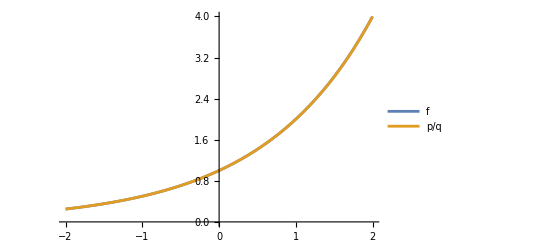

```mathematica
{p,q}=PerformRationalInterpolation[xi, func, 1,3];
PlotCompare[func, p,q ,xi]
```

```mathematica
p//N
q//N
```

-6.-3.16667 x-0.75 x^2-0.0833333 x^3

-6.+x

So long as the function is of one variable, it doesn’t matter what variable is a function of. Although the variable still has to be x in order to plot using the built-in plotter. Working on implementing this feature.

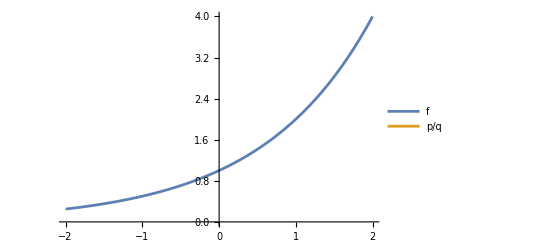

-6.-3.16667 t-0.75 t^2-0.0833333 t^3

-6.+t

```mathematica
func=N[2^t,100];
xi=Table[i,{i,-2,2,1}];
{p,q}=PerformRationalInterpolation[xi, func, 1,3];
PlotCompare[(func/.t->x),p,q,xi]
p//N
q//N
```

Even though the package can extrapolate to any valid degree, it does not guarantee that the polynomial  approximates the function accurately, some care is required when deciding on a n,m to extrapolate to.

{-2,-1,0,1,2}

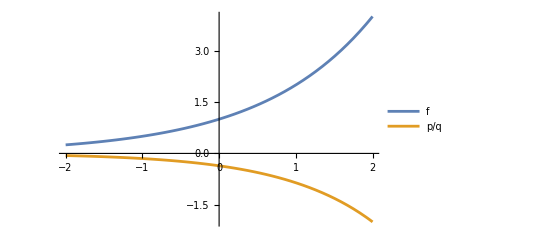

```mathematica
func=N[2^x,100];
xi=Table[i,{i,-2,2,1}]
{p,q}=PerformRationalInterpolation[xi, func, 3,2];
PlotCompare[func, p,q,xi]
```

Example 2 with a more complicated function

Cos[x]-0.5 Sin[x]

{-π,-(3 π)/4,-π/2,-π/4,0,π/4,π/2,(3 π)/4,π}

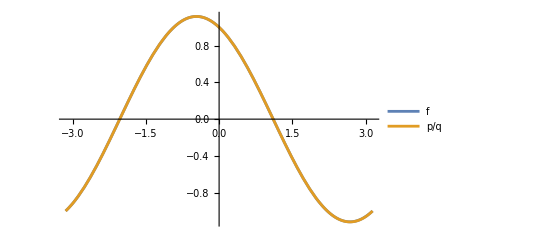

```mathematica
func=N[Cos[x]-(1/2)Sin[x],200];
func//N
xi=Table[i,{i,-Pi,Pi,Pi/4}]
{p,q}=PerformRationalInterpolation[xi, func, 4,4];
PlotCompare[func, p,q,xi]
```

```mathematica
p//N
q// N
```

667.209-304.614 x-315.359 x^2+26.2119 x^3+13.9481 x^4

667.209+28.8199 x+32.6227 x^2+1.7319 x^3+x^4

#### Invalid Interpolation

This package can only work on functions with one variable

```mathematica
func=N[2^x + t ,100]; 
xi=Table[i,{i,-2,2,1}]
PerformRationalInterpolation[xi, func, 2,2]
```

{-2,-1,0,1,2}

Only provide an equation with one variable please

$Aborted

Standard restrictions apply to this set of interpolations as well

```mathematica
func=N[2^x-1,100]; 
xi=Table[i,{i,-2,2,1}]
PerformRationalInterpolation[xi, func, 2,2]
```

{-2,-1,0,1,2}

y points contain 0! This is not supported... Abort!

$Aborted

Some inputs of (x,y) may cause TTR to terminate early, this will simply raise an error